# Determine Solution to U(u)

```mathematica
SetDirectory["/home/steffen/working/calculations/mathematica/Fermions Lattice/data"];
```

```mathematica
SetOptions[Plot,PlotRange->Full,PlotStyle->Evaluate[Directive[#,Thickness[.005]]&/@{Blue,Red}],FrameStyle->Thickness[.005],FrameLabel->{"x","y"},PlotLabel->"Caption",Frame->True,Axes->False];
SetOptions[ListLinePlot,PlotRange->Full,PlotStyle->Evaluate[Directive[#,Thickness[.005]]&/@{Blue,Red}],FrameStyle->Thickness[.005],FrameLabel->{"x","y"},PlotLabel->"Caption",Frame->True,Axes->False];
```

## Equations of motion

```mathematica
f[u_]=1-u^4;
eqU[u_]=U''[u]+(f'[u]/f[u]-1/u)U'[u]+B/f[u] U[u];
```

## Asymptotic at the horizon u_H=1 up to 4^th order

```mathematica
Clear[a,α];
```

### Index and Expansion

```mathematica
hord=6;
UH[u_]=(u-1)^α Sum[a[i](u-1)^i,{i,0,hord}];
```

### Calculation of horizon expansion

```mathematica
expansion=(u-1)^-α eqU[u]/.U->Function[u,Evaluate[UH[u]]];
```

```mathematica
hU=Simplify[Series[expansion,{u,1,hord}]];
Coefficient[hU,u-1,-2]
```

α^2 a[0]

```mathematica
α=0;
a[0]=CU;
Simplify[Coefficient[hU,u-1,-2]]
```

0

```mathematica
For[i=1,i≤hord,i++,
solution=Solve[Coefficient[hU,u-1,i-2]==0,a[i]][[1]];
a[i]=Simplify[a[i]/.solution];
Print[{i,Simplify[Coefficient[hU,u-1,i-2]]}];
]
```

{1,0}

{2,0}

{3,0}

{4,0}

{5,0}

{6,0}

```mathematica
Simplify[Series[expansion,{u,1,hord-2}]]
```

O[u-1]^5

### Write out asymptotic expansion to external file

```mathematica
stream=OpenWrite["AsymptoticU6.dat"];
Write[stream,Table[a[i],{i,0,hord}]];
Close[stream];
```

## Asymptotic at the boundary u_B=0 up to 4^th order

```mathematica
Clear[a,β];
```

### Index and Expansion

```mathematica
hord=2;
UB[u_]=u^β Sum[a[i] u^i,{i,0,hord}];
```

### Calculation of horizon expansion

```mathematica
expansion=u^-β eqU[u]/.U->Function[u,Evaluate[UB[u]]];
```

```mathematica
hU=Simplify[Series[expansion,{u,0,hord}]];
Coefficient[hU,u,-2]
```

(-2+β) β a[0]

### New try with U(u)=(CU1+CU2 u^2)UB(u) and using U(0)=0

```mathematica
Clear[a,UB]
```

```mathematica
hord=4;
UB[u_]=CUB u^2 Sum[a[i] u^i,{i,0,hord}];
```

```mathematica
expansion=eqU[u]/.U->Function[u,Evaluate[UB[u]]];
```

```mathematica
hU=Simplify[Series[expansion,{u,0,hord}]];
Coefficient[hU,u,-1]
```

0

```mathematica
For[i=0,i≤hord,i++,
solution=Solve[Coefficient[hU,u,i]==0,a[i]][[1]];
a[i]=Simplify[a[i]/.solution];
Print[{i,Simplify[Coefficient[hU,u,i]]}];
]
```

{0,0}

{1,0}

{2,0}

{3,0}

{4,0}

```mathematica
UB[u]
```

CUB u^2 (a[0]-1/8 B u^2 a[0]+1/192 (64+B^2) u^4 a[0])

## Solving equations of motion

### Asymptotics near the horizon u_H

```mathematica
hord=4;
α=0;
asymptoticU=ReadList["AsymptoticU6.dat"][[1]];
For[i=0,i≤ hord,i++,
a[i]=asymptoticU[[i+1]]
]
UH[u_,B_]=(u-1)^α Sum[a[i](u-1)^i,{i,0,hord}]/.CU->1;
DUH[u_,B_]=D[UH[u,B],u];
```

### Integration to boundary u_B = 0

```mathematica
IntegrateEOM[EOMΦ_,Φ_,ΦH_,DΦH_,B_,init_,end_]:=
Block[{eomΦ,BoundaryConditionΦ,DBoundaryConditionΦ,solution},
eomΦ=EOMΦ[arg];
BoundaryConditionΦ=ΦH[init,B];
DBoundaryConditionΦ=DΦH[init,B];
solution=NDSolve[{eomΦ==0,Φ[init]==BoundaryConditionΦ,Φ'[init]==DBoundaryConditionΦ},Φ,{arg,end,init},MaxSteps->∞,PrecisionGoal->12,AccuracyGoal->∞][[1]]
]
```

```mathematica
IntegrateToBoundary[EOMΦ_,Φ_,ΦH_,DΦH_,B_,init_,end_]:=
Block[{eomΦ,BoundaryConditionΦ,DBoundaryConditionΦ,solution},
eomΦ=EOMΦ[arg];
BoundaryConditionΦ=ΦH[init,B];
DBoundaryConditionΦ=DΦH[init,B];
solution=NDSolve[{eomΦ==0,Φ[init]==BoundaryConditionΦ,Φ'[init]==DBoundaryConditionΦ},Φ,{arg,end,init},MaxSteps->∞,PrecisionGoal->12,AccuracyGoal->∞][[1]];
{Φ[end],Φ'[end]}/.solution
]
```

```mathematica
SolutionAtBoundary[EOMΦ_,Φ_,ΦH_,DΦH_,B_,init_,end_,ϵ_,n_]:=
Block[{Φ1,Φ2,solution,fit,BΦ},
solution=IntegrateEOM[EOMΦ,Φ,ΦH,DΦH,B,init,end];
Φ1=Φ[end]/.solution;
fit=FindFit[{#,(Φ[#]/.solution)-Φ1}&/@Range[end,n ϵ,ϵ],{BΦ u^2},BΦ,u];
Φ2=BΦ/.fit;
{Φ1,Φ2}
]
```

## Determine optimal values for uinit, uend, ϵ and n

```mathematica
B=1;
```

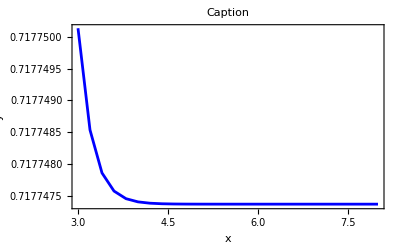

```mathematica
Table[{i,IntegrateToBoundary[eqU,U,UH,DUH,B,1-10^-4,10^-i][[1]]},{i,3,8,.2}];
ListLinePlot[%]
```

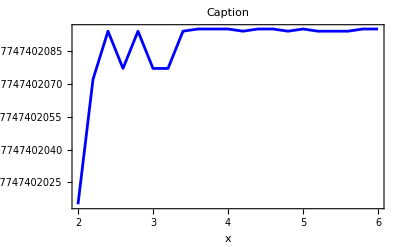

```mathematica
Table[{i,IntegrateToBoundary[eqU,U,UH,DUH,B,1-10^-i,10^-4][[1]]},{i,2,6,.2}];
ListLinePlot[%]
```

### Finding the optimal values for ϵ and n

```mathematica
uinit=1-10^-4;
uend=10^-4;
n=100;
ϵ=10^-3;
```

```mathematica
solf=IntegrateEOM[eqU,U,UH,DUH,B,uinit,uend];
solb=SolutionAtBoundary[eqU,U,UH,DUH,B,uinit,uend,ϵ,n]
```

{0.717747,1.19223}

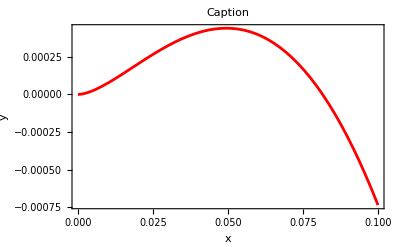

```mathematica
Plot[(U[u]/.solf)-(solb[[1]]+solb[[2]] u^2),{u,uend,.1}]
```

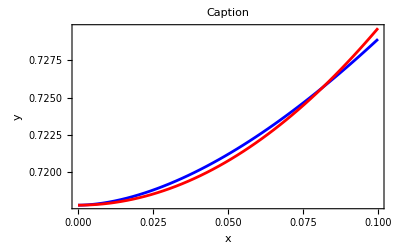

```mathematica
Plot[{(U[u]/.solf),solb[[1]]+solb[[2]] u^2},{u,uend,.1}]
```

### Check horizon asymptotic

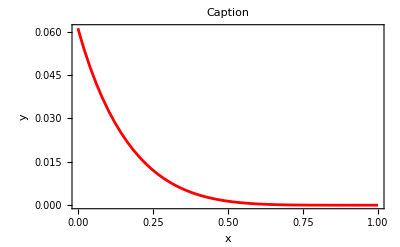

```mathematica
Plot[(U[u]/.solf)-UH[u,B],{u,uinit,uend}]
```

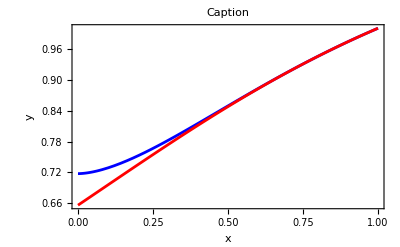

```mathematica
Plot[{U[u]/.solf,UH[u,B]},{u,uinit,uend}]
```

## Find critical value B=B_c where U(0)=0

```mathematica
Clear[B]
```

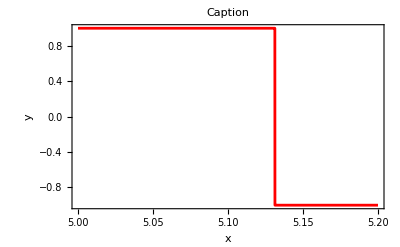

```mathematica
Plot[Sign[IntegrateToBoundary[eqU,U,UH,DUH,B,uinit,uend][[1]]],{B,5,5.2}]
```

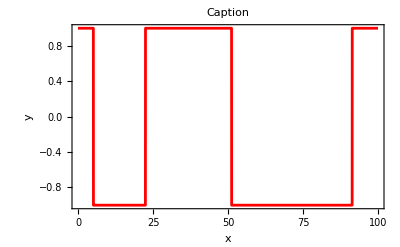

```mathematica
Plot[Sign[IntegrateToBoundary[eqU,U,UH,DUH,B,uinit,uend][[1]]],{B,0,100}]
```

### Weird error

```mathematica
Table[IntegrateToBoundary[eqU,U,UH,DUH,B,uinit,uend],{B,{5.12}}]
IntegrateToBoundary[eqU,U,UH,DUH,5.12,uinit,uend]
```

{{0.00118073,0.000325119}}

NDSolve::ndnum: Encountered non-numerical value for a derivative at arg == 0.9999.

ReplaceAll::reps: B U[arg]/1 - Power[« 2 »] + (-1/arg - 4 arg^3/Plus[« 2 »]) SuperscriptBox[U[9999/10000] == 0.9998719976962092`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{U[1/10000],U'[1/10000]}/.{(B U[arg])/(1-arg^4)+(-1/arg-(4 arg^3)/(1-arg^4)) U'[arg]+U''[arg]==0,U[9999/10000]==0.999872,U'[9999/10000]==1.28005}

```mathematica
binsearch[start_,end_,bisections_,func_]:=
Module[{sign1,interval,dir,pos,sign2,i},
sign1=Sign[func[start]];
interval=end-start;
dir=1;
pos=start;
For[i=1,i≤bisections,i++,
pos=pos+dir interval/2^i;
sign2=Sign[func[pos]];
If[sign2≠sign1,dir=-dir];
sign1=sign2;
];
{pos,func[pos]}
]
```

```mathematica
func[B_]:=IntegrateToBoundary[eqU,U,UH,DUH,B,uinit,uend];
binsearch[5.131,5.132,50,func];
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at arg == 0.9999.

ReplaceAll::reps: B U[arg]/1 - Power[« 2 »] + (-1/arg - 4 arg^3/Plus[« 2 »]) SuperscriptBox[U[9999/10000] == 0.9998717227000792`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at arg == 0.9999.

ReplaceAll::reps: B U[arg]/1 - Power[« 2 »] + (-1/arg - 4 arg^3/Plus[« 2 »]) SuperscriptBox[U[9999/10000] == 0.9998717102002559`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at arg == 0.9999.

General::stop: Further output of NDSolve :: ndnum will be suppressed during this calculation.

ReplaceAll::reps: B U[arg]/1 - Power[« 2 »] + (-1/arg - 4 arg^3/Plus[« 2 »]) SuperscriptBox[U[9999/10000] == 0.9998717039503443`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
Table[IntegrateToBoundary[eqU,U,UH,DUH,B,uinit,uend],{B,{5.1312677905711,5.1312677905712}}]
```

{{1.15779×10^-14,0.000320352},{-3.05119×10^-16,0.000320352}}

### Write out solution for B_c=5.1312677905712

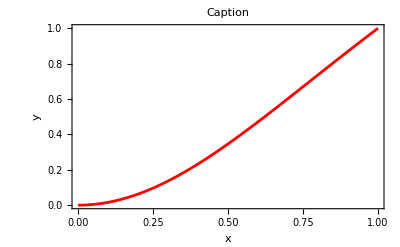

```mathematica
B=5.1312677905712;
solution=IntegrateEOM[eqU,U,UH,DUH,B,uinit,uend];
Plot[U[u]/.solution,{u,uinit,uend}]
```

```mathematica
stream=OpenWrite["SolutionU.dat"];
Write[stream,solution];
Close[stream];
```